```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## Top - G - G vertex

in total: 1 Particles insertion

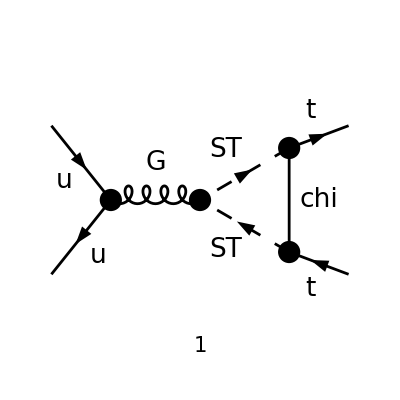

```mathematica
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings];
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 1 Particles amplitude

-(2 √π √aS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(γ·q).(γ̄)^6.(φ(-p2,MT)) ((φ(-k2)).GS.(γ·p1).(φ(k1))-(φ(-k2)).GS.(γ·p2).(φ(k1))+2 (φ(-k2)).GS.(γ·q).(φ(k1))))/((p1+p2)^2 (q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)
```

-1/(p1+p2)^2 4 ⅈ π^(5/2) √aS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (φ(-k2)).GS.γ^($AL($247)).(φ(k1)) (φ(p1,MT)).γ^($AL($247)).(γ̄)^6.(φ(-p2,MT))+1/2 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT)) ((φ(-k2)).GS.(γ·p1).(φ(k1))-(φ(-k2)).GS.(γ·p2).(φ(k1)))+C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))-C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampC)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-1/(p1+p2)^2 2 ⅈ π^2 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (φ(-k2)).GS.γ^($AL($247)).(φ(k1)) (φ(p1,MT)).γ^($AL($247)).(γ̄)^6.(φ(-p2,MT))+1/2 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT)) ((φ(-k2)).GS.(γ·p1).(φ(k1))-(φ(-k2)).GS.(γ·p2).(φ(k1)))+C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))-C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))

```mathematica
ampEsimp=ampE//.{PaVe[0,0,a_,b_,c_,d_]->C00,PaVe[1,1,a_,b_,c_,d_]->C11,PaVe[1,2,a_,b_,c_,d_]->C12,PaVe[1,a_,b_,c_,d_]->C1}
```

-1/(p1+p2)^2 2 ⅈ π^2 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (C00 (φ(-k2)).GS.γ^($AL($247)).(φ(k1)) (φ(p1,MT)).γ^($AL($247)).(γ̄)^6.(φ(-p2,MT))+1/2 C1 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT)) ((φ(-k2)).GS.(γ·p1).(φ(k1))-(φ(-k2)).GS.(γ·p2).(φ(k1)))+C11 ((φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))-C12 ((φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))

```mathematica
Collect[ampEsimp,{C00,C11,C12,C1},Simplify]
```

-(2 ⅈ π^2 C00 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).GS.γ^($AL($247)).(φ(k1)) (φ(p1,MT)).γ^($AL($247)).(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2-(ⅈ π^2 C1 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT)) ((φ(-k2)).GS.(γ·p1).(φ(k1))-(φ(-k2)).GS.(γ·p2).(φ(k1))))/(p1+p2)^2-(2 ⅈ π^2 C11 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))/(p1+p2)^2+(2 ⅈ π^2 C12 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).GS.(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).GS.(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))/(p1+p2)^2

```mathematica
Collect[ampEsimp,{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[Momentum[p1,D],D],DiracGamma[Momentum[p2,D],D],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},Simplify]
```

-1/(p1+p2)^2 2 ⅈ π^2 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (C00 (φ(-k2)).GS.γ^($AL($247)).(φ(k1)) (φ(p1,MT)).γ^($AL($247)).(γ̄)^6.(φ(-p2,MT))-1/2 (φ(-k2)).GS.(γ·p2).(φ(k1)) (C1 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT))-2 C11 (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))+2 C12 (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)))+(φ(-k2)).GS.(γ·p1).(φ(k1)) (1/2 C1 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT))+C11 (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))-C12 (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))

```mathematica
Collect[ampEsimp,{C00,(C1+2 C11),(C1+ 2 C12)},Simplify]
```

-(2 ⅈ π^2 C00 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).GS.γ^($AL($247)).(φ(k1)) (φ(p1,MT)).γ^($AL($247)).(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2-1/(p1+p2)^2 2 ⅈ π^2 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).GS.(γ·p1).(φ(k1)) (1/2 C1 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT))+C11 (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))-C12 (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)))-1/2 (φ(-k2)).GS.(γ·p2).(φ(k1)) (C1 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT))-2 C11 (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))+2 C12 (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))))

```mathematica
FullSimplify[%]
```

-1/(p1+p2)^2 2 ⅈ π^2 GS yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (C00 (φ(-k2)).GS.γ^($AL($247)).(φ(k1)) (φ(p1,MT)).γ^($AL($247)).(γ̄)^6.(φ(-p2,MT))-1/2 (φ(-k2)).GS.(γ·p2).(φ(k1)) (C1 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT))-2 C11 (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))+2 C12 (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)))+(φ(-k2)).GS.(γ·p1).(φ(k1)) (1/2 C1 (φ(p1,MT)).(γ·(p1-p2)).(γ̄)^6.(φ(-p2,MT))+C11 (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))-C12 (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))))

### Default Values (High Mass Limit)

```mathematica
ampEeft=Limit[PaXEvaluate[ampE,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{s,0,0},{MT,0,0}}],mChi->mST]//Simplify;
Collect[ampEeft,{Epsilon,mST},Simplify]
```

(ⅈ GS yDM^2 T_Col2Col3^Glu1 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6))/(192 π^2 mST^2)+(ⅈ GS yDM^2 γ^μ.(γ̄)^6 (ℽ-log((4 π μ^2)/mST^2)) T_Col2Col3^Glu1)/(32 π^2)-(ⅈ GS yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(32 π^2 ε)

```mathematica
C00def=PaXEvaluate[PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]//Simplify
C1def=PaXEvaluate[PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]//Simplify
C11def=PaXEvaluate[PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]//Simplify
C12def=PaXEvaluate[PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{s,0,0}}]//Simplify
```

-((mChi^2-mST^2) (mChi^2 (ε (-3+2 ℽ-2 log(4 π))-2)+2 ε (mST^2-mChi^2) log(μ^2/mST^2)+mST^2 (-2 ℽ ε+ε+2 ε log(4 π)+2))+2 ε mChi^4 log(mChi^2/mST^2))/(128 π^4 ε (mChi-mST)^2 (mChi+mST)^2)

-(-4 mChi^2 mST^2-2 mChi^4 log(mChi^2/mST^2)+3 mChi^4+mST^4)/(64 π^4 (mChi-mST)^3 (mChi+mST)^3)

(-18 mChi^4 mST^2+9 mChi^2 mST^4-6 mChi^6 log(mChi^2/mST^2)+11 mChi^6-2 mST^6)/(288 π^4 (mChi-mST)^4 (mChi+mST)^4)

(-18 mChi^4 mST^2+9 mChi^2 mST^4-6 mChi^6 log(mChi^2/mST^2)+11 mChi^6-2 mST^6)/(576 π^4 (mChi-mST)^4 (mChi+mST)^4)

#### Expressions for the EFT coefficients (high mass limit)

```mathematica
A1 = Collect[FullSimplify[2 Pi^2 yDM^2 (C00def -  MT^2 (C1def +C11def + C12def) + s/2(C11def- C12def))/.{s->0,MT->0,EulerGamma->0,ScaleMu->ScaleMu/(√(4 Pi))}],{Epsilon,Log[a_]},Simplify]
```

(yDM^2 (3 mChi^2-mST^2))/(64 π^2 (mChi^2-mST^2))-(mChi^4 yDM^2 log(mChi^2/mST^2))/(32 π^2 (mChi^2-mST^2)^2)+(yDM^2 log(μ^2/mST^2))/(32 π^2)+yDM^2/(32 π^2 ε)

```mathematica
A2=FullSimplify[-2 Pi^2 yDM^2 (C1def + C11def+C12def)]
```

-(yDM^2 (3 mChi^4 mST^2-6 mChi^2 mST^4-6 mChi^4 mST^2 log(mChi^2/mST^2)+2 mChi^6+mST^6))/(96 π^2 (mChi^2-mST^2)^4)

```mathematica
A3=Collect[FullSimplify[Pi^2 yDM^2  gs(C12def-C11def)],{Log[a_]}]
```

(gs yDM^2 (18 mChi^4 mST^2-9 mChi^2 mST^4-11 mChi^6+2 mST^6))/(576 π^2 (mChi^2-mST^2)^4)+(gs mChi^6 yDM^2 log(mChi^2/mST^2))/(96 π^2 (mChi^2-mST^2)^4)

### High Mass and Degenerate Limit

```mathematica
Collect[Limit[A1,mChi->mST],{Epsilon},Simplify]
```

(yDM^2 log(μ^2/mST^2))/(32 π^2)+yDM^2/(32 π^2 ε)

```mathematica
Collect[Limit[A2,mChi->mST],{Epsilon}]
```

-yDM^2/(192 π^2 mST^2)

```mathematica
Collect[Limit[A3,mChi->mST],{Epsilon}]
```

(gs yDM^2)/(384 π^2 mST^2)